#### functions

```mathematica
connectivityEI[totN_,eR_,means_,gains_]:=If[Or[eR==0,eR==1],
Table[RandomVariate[NormalDistribution[means,gains/Sqrt[totN]],totN],totN],
Module[{eN=Round[eR*totN],iN,meanEE,meanEI,meanIE,meanII},
iN=totN-eN;
If[Length[means]==1,
meanEE=means[[1]];meanEI=-meanEE*eN/iN;meanIE=meanEE;meanII=meanEI,
If[Length[means]==2,
meanEE=means[[1]];meanEI=-meanEE*eN/iN;meanIE=means[[2]];meanII=-meanIE*eN/iN,
If[Length[means]==4,
meanEE=means[[1]];meanEI=means[[2]];meanIE=means[[3]];meanII=means[[4]],]]];
Return[ArrayFlatten[{{Table[RandomVariate[NormalDistribution[meanEE,gains[[1,1]]/Sqrt[(*eN*)totN]],eN],eN],Table[RandomVariate[NormalDistribution[meanEI,gains[[1,2]]/Sqrt[(*iN*)totN]],iN],eN]},{Table[RandomVariate[NormalDistribution[meanIE,gains[[2,1]]/Sqrt[(*eN*)totN]],eN],iN],Table[RandomVariate[NormalDistribution[meanII,gains[[2,2]]/Sqrt[(*iN*)totN]],iN],iN]}}]]]]
```

```mathematica
rk4OdeSolver[velocities_,initials_,domain_,resolution_]:=Module[{positionsOutput=Table[Table[0,Length[initials]],(domain[[2]]-domain[[1]])*resolution+1],positionsPresent=initials,positionsNext,correction1,correction2,correction3,correction4,stepSize=1/resolution},
positionsOutput[[1]]=initials;
Do[correction1=velocities[positionsPresent];
correction2=velocities[positionsPresent+stepSize*correction1/2];
correction3=velocities[positionsPresent+stepSize*correction2/2];
correction4=velocities[positionsPresent+stepSize*correction3];
positionsNext=positionsPresent+stepSize*(correction1/6+correction2/3+correction3/3+correction4/6);
positionsOutput[[idx+1]]=positionsNext;
positionsPresent=positionsNext,
{idx,(domain[[2]]-domain[[1]])*resolution}];
positionsOutput=Transpose[positionsOutput];
Return[positionsOutput]
]
rk4OdeXSolver[velocities_,externals_,initials_,domain_,resolution_]:=
Module[{velocities4,initials4,dimN=Length[initials]},
velocities4[positions4_]:=Join[velocities[positions4[[1;;dimN]]]+externals[positions4[[dimN+1]]],{1}];
initials4=Join[initials,{domain[[1]]}];
Return[rk4OdeSolver[velocities4,initials4,domain,resolution][[1;;dimN]]]]
rk4OdeXSolverSegmenting[velocities_,externals_,initials_,domains_,resolution_]:=Module[{positions=Table[Table[Table[0,(domains[[domainIdx,2]]-domains[[domainIdx,1]])*resolution+1],Length[externals]],{domainIdx,Length[domains]}],initialsT=initials},
Do[positions[[domainIdx]]=rk4OdeXSolver[velocities,externals,initialsT,domains[[domainIdx]],resolution];initialsT=Last[Transpose[positions[[domainIdx]]]](*positionsT[[;;,(domains[[domainIdx,2]]-domains[[domainIdx,1]])*resolution+1]]*),{domainIdx,Length[domains]}];
Return[positions]]
```

```mathematica
crossCorrelationMoment[list1_,list2_,lag_]:=Module[{mean1=Mean[list1],mean2=Mean[list2]},Return[list1[[1;;Length[list1]-lag]].list2[[lag+1;;Length[list2]]]/Sqrt[Total[Norm[list1]^2]]/Sqrt[Total[Norm[list2]^2]]]]
crossCorrelationCumulant[list1_,list2_,lag_]:=Module[{mean1=Mean[list1],mean2=Mean[list2]},Return[(list1[[1;;Length[list1]-lag]]-mean1).(list2[[lag+1;;Length[list2]]]-mean2)/Sqrt[Total[Norm[list1-mean1]^2]]/Sqrt[Total[Norm[list2-mean2]^2]]]]
(*With[{foo=Table[Exp[-idx],{idx,0,10}]},
ListPlot[{Table[{lag,crossCorrelationMoment[foo,foo,lag]},{lag,0,10}],Table[{lag,crossCorrelationCumulant[foo,foo,lag]},{lag,0,10}]}]]*)
```

```mathematica
participationRatio[list_]:=Mean[list]^2/Mean[list^2]
```

```mathematica
save[expression_,filename_]:=Module[{imported},Export[StringJoin[NotebookDirectory[],filename,".mx"],expression];imported=Import[StringJoin[NotebookDirectory[],filename,".mx"]];
If[imported==expression,Print[StringJoin["saved to ",filename]]]]
```

#### 1 instance details

```mathematica
totN=100;
eR=0.8;
means={0.18};
gains=Table[3.,2];
connectivity=connectivityEI[totN,eR,means,Table[gains,2]];
externalR=0.2;
connectivityExternal=RandomVariate[BernoulliDistribution[externalR],totN]*1.(*Join[RandomVariate[BernoulliDistribution[externalR],Round[totN*eR]],Table[0,totN-Round[totN*eR]]]*1.*);
freq=8/50;
timeIsLabeled={{{0,25},1},{{25,50},0}};
externalStrength=3.;
```

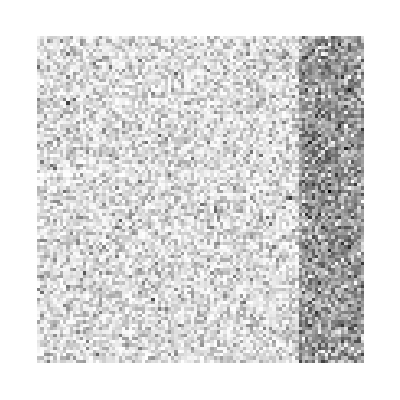
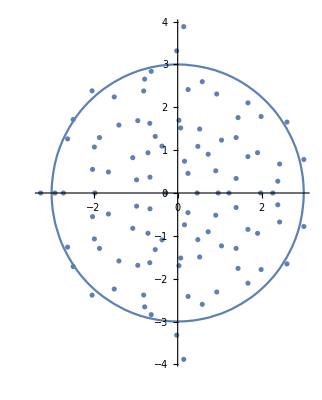

```mathematica
{ArrayPlot[connectivity],Show[ComplexListPlot[Eigenvalues[connectivity]],ContourPlot[x^2+y^2==(eR*gains[[1]]^2+(1-eR)*gains[[2]]^2),{x,-10,10},{y,-10,10}]]}
```

```mathematica
nonlinearity1=Identity;
nonlinearity2=(*With[{r=0.1},Function[x,If[x>0,(2-r)Tanh[x/(2-r)],r*Tanh[x/r]]]]*)Tanh;
velocities[positions_]:=-positions+nonlinearity1[connectivity.nonlinearity2[positions]];
spikeTimes=Flatten[Table[Sort[RandomVariate[UniformDistribution[timeIsLabeled[[timeILabeledIdx,1]]],Round[(timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]])*timeIsLabeled[[timeILabeledIdx,2]]*freq]]],{timeILabeledIdx,Length[timeIsLabeled]}]];
externals[time_]:=connectivityExternal*externalStrength*Total[Exp[-(time-spikeTimes)^2/2/0.5^2]];
resolution=24(*60*);
initials=RandomVariate[NormalDistribution[0,1],totN]+Table[0.,{idx,totN}];
states=nonlinearity2[rk4OdeXSolverSegmenting[velocities,externals,initials,timeIsLabeled[[;;,1]],resolution]];
```

General::munfl: Exp[-709.132] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-710.702] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

General::munfl: Exp[-718.617] is too small to represent as a normalized machine number; precision may be lost.

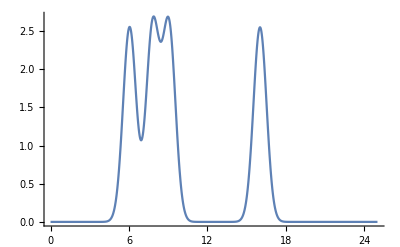
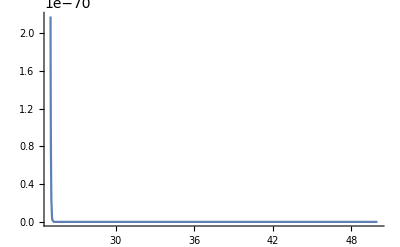
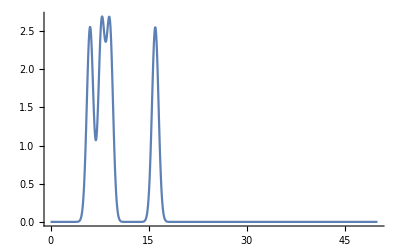
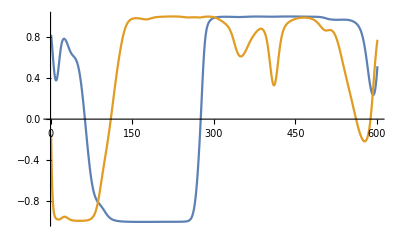
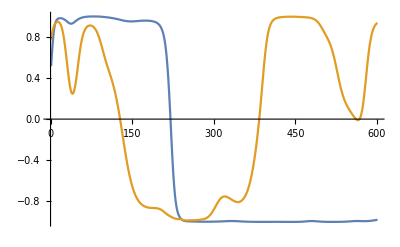
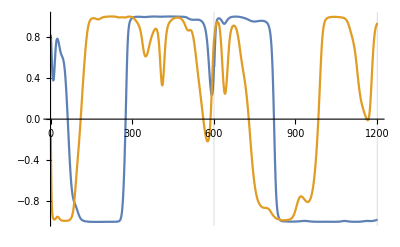
timeI | {{0,25},1} | {{25,50},0} | all
ext | -Graphics- | -Graphics- | -Graphics-
state | -Graphics- | -Graphics- | -Graphics-

```mathematica
characteristicIdxs={Position[connectivityExternal,0.][[1,1]],Position[connectivityExternal,1.][[1,1]]};
statesA=Table[states[[timeILabeledIdx,characteristicIdxs,Table[time*resolution+1,{time,0,timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]],1/resolution}]]],{timeILabeledIdx,Length[timeIsLabeled]}];
Grid[Join[{Join[{"timeI"},timeIsLabeled,{"all"}]},{Join[{"ext"},Table[Plot[Mean[externals[time]]/externalR,Join[{time},timeIsLabeled[[timeILabeledIdx,1]]],PlotRange->All],{timeILabeledIdx,Length[timeIsLabeled]}],{Plot[Mean[externals[time]]/externalR,{time,First[timeIsLabeled][[1,1]],Last[timeIsLabeled][[1,2]]},PlotRange->All]}]},{Join[{"state"},Table[ListPlot[statesA[[timeILabeledIdx]],Joined->True,PlotRange->All],{timeILabeledIdx,Length[timeIsLabeled]}],{ListPlot[Map[Function[table,Apply[Join,table]],Transpose[statesA]],Joined->True,GridLines->{(timeIsLabeled[[;;,1,2]]-timeIsLabeled[[1,1,1]])*resolution+1,{}}]}]}]]
```

```mathematica
acs=Table[Table[Table[{lag,crossCorrelationMoment[states[[timeILabeledIdx,idx]],states[[timeILabeledIdx,idx]],lag*resolution]},{lag,0,timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]](*,Floor[(timeI[[2]]-timeI[[1]])/100]*)}],{idx,totN}],{timeILabeledIdx,Length[timeIsLabeled]}];
popMeanAc=Table[Map[Mean,Transpose[acs[[timeILabeledIdx]]]],{timeILabeledIdx,Length[timeIsLabeled]}];
```

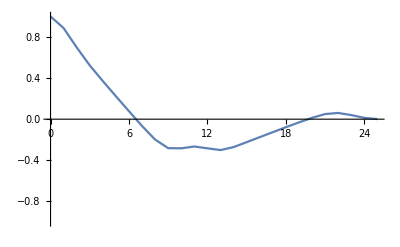
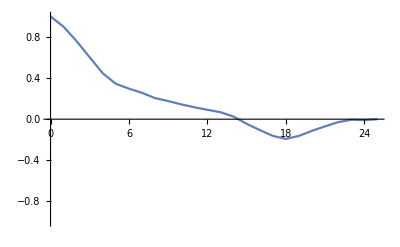
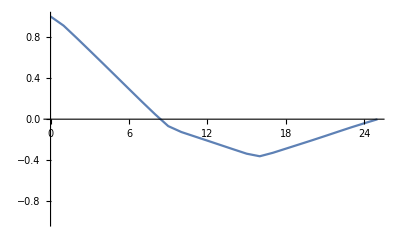
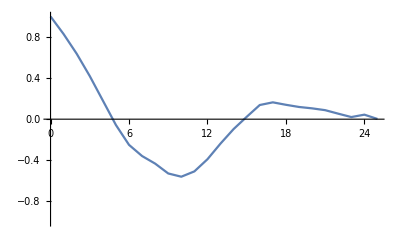
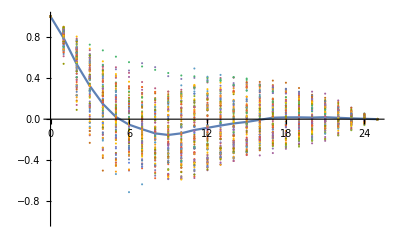
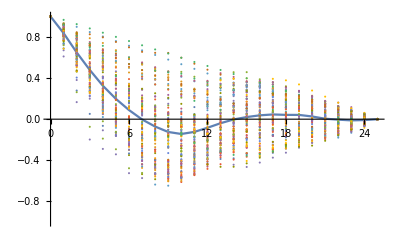
units | {-Graphics-,-Graphics-} | {-Graphics-,-Graphics-}
means | -Graphics- | -Graphics-

```mathematica
Grid[{Join[{"units"},Table[Table[ListPlot[acs[[timeILabeledIdx,idx]],Joined->True,PlotRange->{-1,1}],{idx,characteristicIdxs}],{timeILabeledIdx,Length[timeIsLabeled]}]],
(*Table[ListLogLogPlot[Abs[acs[[idx]]],Joined->True,PlotRange->{-1,1}],{idx,characteristicIdxs}]*)
Join[{"means"},Table[Show[ListPlot[popMeanAc[[timeILabeledIdx]],PlotRange->{-1,1},Joined->True],ListPlot[acs[[timeILabeledIdx]]]],{timeILabeledIdx,Length[timeIsLabeled]}]]}]
```

```mathematica
ccs=Table[Table[Table[{lag,crossCorrelationMoment[states[[timeILabeledIdx,1]],states[[timeILabeledIdx,idx]],lag*resolution]},{lag,0,timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]](*,Floor[(timeI[[2]]-timeI[[1]])/100]*)}],{idx,totN}],{timeILabeledIdx,Length[timeIsLabeled]}];
popMeanCc=Table[Map[Mean,Transpose[ccs[[timeILabeledIdx]]]],{timeILabeledIdx,Length[timeIsLabeled]}];
```

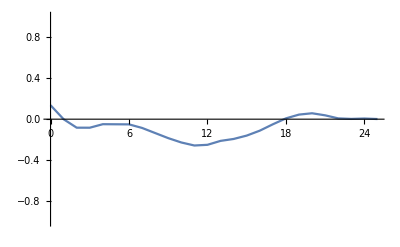
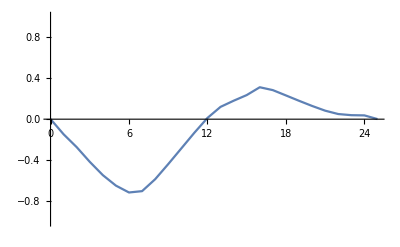
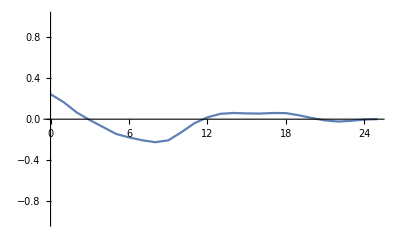
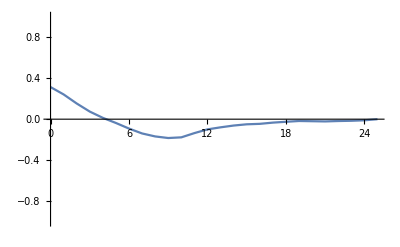
units | {-Graphics-,-Graphics-} | {-Graphics-,-Graphics-}
means | -Graphics- | -Graphics-

```mathematica
Grid[{Join[{"units"},Table[Table[ListPlot[ccs[[timeILabeledIdx,idx]],Joined->True,PlotRange->{-1,1}],{idx,characteristicIdxs}],{timeILabeledIdx,Length[timeIsLabeled]}]],
(*Table[ListLogLogPlot[Abs[ccs[[idx]]],Joined->True,PlotRange->{-1,1}],{idx,characteristicIdxs}]*)
Join[{"means"},Table[ListPlot[popMeanCc[[timeILabeledIdx]],PlotRange->{-1,1},Joined->True],{timeILabeledIdx,Length[timeIsLabeled]}]]}]
```

```mathematica
pcs=Table[Transpose[PrincipalComponents[Transpose[states[[timeILabeledIdx]]]]],{timeILabeledIdx,Length[timeIsLabeled]}];
vars=Table[Map[Variance,pcs[[timeILabeledIdx]]],{timeILabeledIdx,Length[timeIsLabeled]}];
pr=Table[participationRatio[vars[[timeILabeledIdx]]],{timeILabeledIdx,Length[timeIsLabeled]}];
(*With[{foo=Map[Variance,Transpose[PrincipalComponents[Transpose[positions]]]],bar=Eigenvalues[Table[(positions[[idx1]]-Mean[positions[[idx1]]]).(positions[[idx2]]-Mean[positions[[idx2]]]),{idx1,totN},{idx2,totN}]]},
ListPlot[bar/foo,PlotRange->All]]*)
```

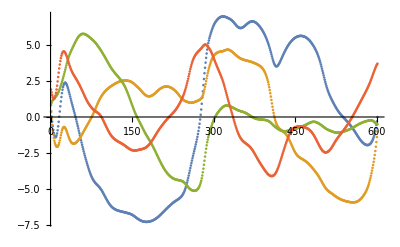
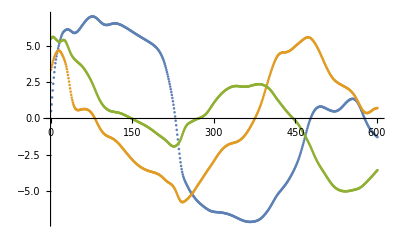
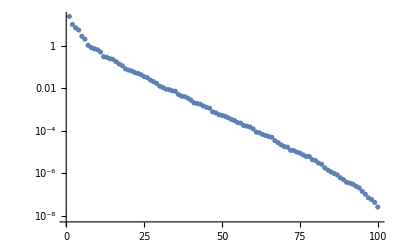
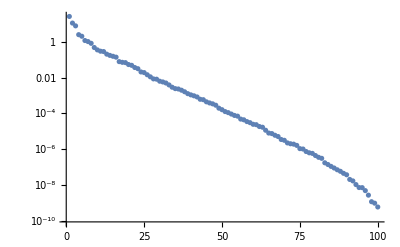
pcs | -Graphics- | -Graphics-
{vars,pr} | {-Graphics-,0.0424695} | {-Graphics-,0.0347237}

```mathematica
Grid[{Join[{"pcs"},Table[ListPlot[pcs[[timeILabeledIdx,1;;Round[pr[[timeILabeledIdx]]*totN]]],PlotRange->All],{timeILabeledIdx,Length[timeIsLabeled]}]],
Join[{{"vars","pr"}},Table[{ListLogPlot[vars[[timeILabeledIdx]],PlotRange->All],pr[[timeILabeledIdx]]},{timeILabeledIdx,Length[timeIsLabeled]}]]}]
```

#### J average - relaxing/relaxed

```mathematica
totN=100(*300*);
eR=0.8;
means={0.18};
gains=Table[3.,2];
externalR=0.2;
freq=8/50;
externalStrength=1.;
timeIsLabeled={{{0,20},1},{{20,40},1},{{40,60},0},{{60,80},0}};
resolution=24(*60*);
nonlinearity1=Identity;
nonlinearity2=(*With[{r=0.1},Function[x,If[x>0,(2-r)Tanh[x/(2-r)],r*Tanh[x/r]]]]*)Tanh;
instanceN=20(*100*);
popMeanAcs=Table[Table[Table[0,{lag,0,timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]]}],instanceN],{timeILabeledIdx,Length[timeIsLabeled]}];
prs=Table[Table[Table[0,instanceN],{timeILabeledIdx,Length[timeIsLabeled]}],3];
Do[connectivity=connectivityEI[totN,eR,means,Table[gains,2]];
velocities[positions_]:=-positions+nonlinearity1[connectivity.nonlinearity2[positions]];rotationEv=Inverse[Transpose[Eigenvectors[connectivity]]];
connectivityExternal=RandomVariate[BernoulliDistribution[externalR],totN]*1.;
spikeTimes=Flatten[Table[Sort[RandomVariate[UniformDistribution[timeIsLabeled[[timeILabeledIdx,1]]],Round[(timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]])*timeIsLabeled[[timeILabeledIdx,2]]*freq]]],{timeILabeledIdx,Length[timeIsLabeled]}]];
externals[time_]:=connectivityExternal*externalStrength*Total[Exp[-(time-spikeTimes)^2/2/0.5^2]];
initials=RandomVariate[NormalDistribution[0,1],totN]+Table[0.,{idx,totN}];states=nonlinearity2[rk4OdeXSolverSegmenting[velocities,externals,initials,timeIsLabeled[[;;,1]],resolution]];
Do[acsT=Table[Table[{lag,crossCorrelationMoment[states[[timeILabeledIdx,idx]],states[[timeILabeledIdx,idx]],lag*resolution]},{lag,0,timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]],1}],{idx,totN}];
popMeanAcs[[timeILabeledIdx,instanceIdx]]=Map[Mean,Transpose[acsT]];
prs[[1,timeILabeledIdx,instanceIdx]]=participationRatio[Map[Variance,Transpose[PrincipalComponents[Transpose[states[[timeILabeledIdx]](*Tanh[positions]*)]]]]];
prs[[2,timeILabeledIdx,instanceIdx]]=participationRatio[Map[Variance,rotationEv.states[[timeILabeledIdx]]]];
prs[[3,timeILabeledIdx,instanceIdx]]=participationRatio[Map[Variance,states[[timeILabeledIdx]]]],{timeILabeledIdx,Length[timeIsLabeled]}],{instanceIdx,instanceN}]
(*save[popMeanAcs,"popMeanAcs"]
save[{prsPca,prsEv,prsNatural},"prs"]*)
```

General::munfl: Exp[-725.397] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-969.313] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1158.73] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
meanAc=Table[Map[Mean,Transpose[popMeanAcs[[timeILabeledIdx]]]],{timeILabeledIdx,Length[timeIsLabeled]}];
statsPrs=Table[Table[{Mean[prs[[prTypeIdx,timeILabeledIdx]]],StandardDeviation[prs[[prTypeIdx,timeILabeledIdx]]]},{timeILabeledIdx,Length[timeIsLabeled]}],{prTypeIdx,3}];
```

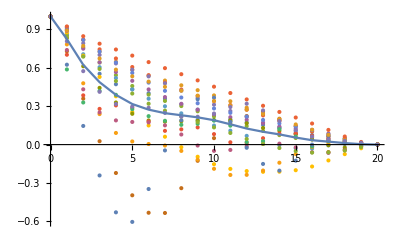
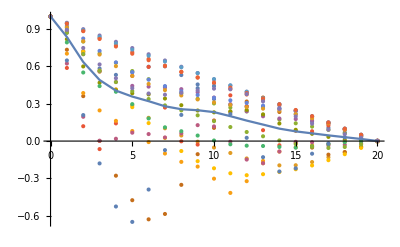
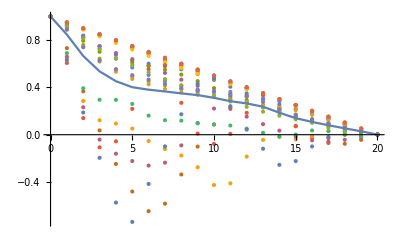
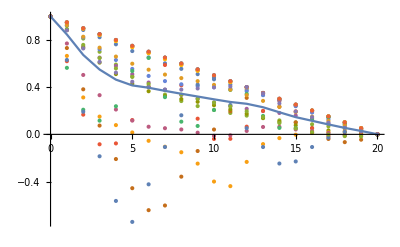
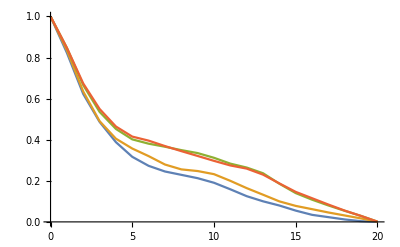
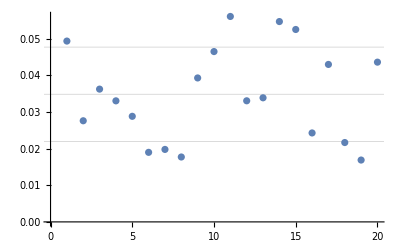
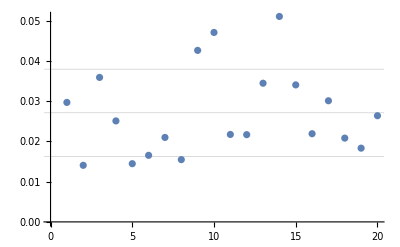
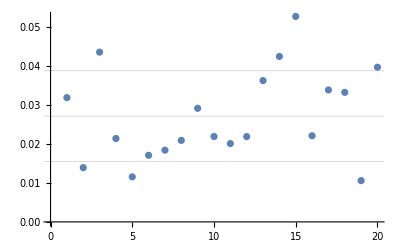
timeI | {{0,20},1} | {{20,40},1} | {{40,60},0} | {{60,80},0} | all
ac | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
pr(pca) | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
pr(ev) | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
pr(nat) | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[Transpose[Join[{{"timeI","ac","pr(pca)", "pr(ev)", "pr(nat)"}},
Table[Join[{timeIsLabeled[[timeILabeledIdx]],
Show[ListPlot[popMeanAcs[[timeILabeledIdx]],PlotRange->All],ListPlot[meanAc[[timeILabeledIdx]],PlotRange->All,Joined->True]]},Table[ListPlot[prs[[prTypeIdx,timeILabeledIdx]],GridLines->{{}, statsPrs[[prTypeIdx,timeILabeledIdx,1]]+{-1,0,1}*statsPrs[[prTypeIdx,timeILabeledIdx,2]]}],{prTypeIdx,3}]],{timeILabeledIdx,Length[timeIsLabeled]}],{Join[{"all",ListPlot[meanAc,Joined->True]},Table[ListPlot[Table[{Mean[timeIsLabeled[[timeILabeledIdx,1]]],Apply[Around,statsPrs[[idx,timeILabeledIdx]]]},{timeILabeledIdx,Length[timeIsLabeled]}],PlotRange->{{0,0.15},{0,0.5},{0,1}}[[idx]]],{idx,3}]]}]]]
```

#### classifiability - different freqs

```mathematica
totN=500(*300*);
eR=0.8;
means={0.18};
gains=Table[1.01,2];
Print[StringJoin["spectral radius is ",ToString[Sqrt[eR*gains[[1]]^2+(1-eR)*gains[[2]]^2]]]]
externalR=0.2;
nonlinearity1=Identity;
nonlinearity2=(*With[{r=0.1},Function[x,If[x>0,(2-r)Tanh[x/(2-r)],r*Tanh[x/r]]]]*)Tanh;
freqs={4,8}/10(*{8,16}/50*);
externalStrength=1.;
timeIsLabeled={{{0,20},1},{{20,40},0},{{40,60},0}}(*{{{0,30},1},{{30,60},1},{{60,90},0},{{90,120},0},{{120,150},0}}*);
classifiedExternalConditions={1,0};
resolution=24(*60*);
externalInstanceN=10;
trainingInstanceR=0.5(*Round[externalInstanceN*0.5]*);
connectivitysInstanceN=8;
```

```mathematica
means=;
rmss=;
testResults=;
Do[connectivity=connectivityEI[totN,eR,means,Table[gains,2]];
connectivityExternal=RandomVariate[BernoulliDistribution[externalR],totN]*1.;
velocities[positions_]:=-positions+nonlinearity1[connectivity.nonlinearity2[positions]];
statesLabeledTAll=Table[Table[Table[(Table[Table[0,(timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]])*resolution+1],totN]->0),{timeILabeledIdx,Length[timeIsLabeled]}],externalInstanceN],Length[freqs]];
Do[Do[spikeTimes=Flatten[Table[Sort[RandomVariate[UniformDistribution[timeIsLabeled[[timeILabeledIdx,1]]],Round[(timeIsLabeled[[timeILabeledIdx,1,2]]-timeIsLabeled[[timeILabeledIdx,1,1]])*timeIsLabeled[[timeILabeledIdx,2]]*freqs[[conditionIdx]]]]],{timeILabeledIdx,Length[timeIsLabeled]}]];
externals[time_]:=connectivityExternal*(freqs[[1]]/freqs[[conditionIdx]]*externalStrength)*Total[Exp[-(time-spikeTimes)^2/2/0.5^2]];
initials=RandomVariate[NormalDistribution[0,1],totN]+Table[0.,{idx,totN}];statesLabeledAll[[conditionIdx,externalInstanceIdx,;;,1]]=nonlinearity2[rk4OdeXSolverSegmenting[velocities,externals,initials,timeIsLabeled[[;;,1]],resolution]];statesLabeledAll[[conditionIdx,externalInstanceIdx,;;,2]]=freqs[[conditionIdx]]
,{conditionIdx,Length[freqs]}],{externalInstanceIdx,externalInstanceN}];
(*****************)
,{connectivitysInstanceIdx,connectivitysInstanceN}]
(*save[{connectivity,connectivityExternal},"connectivities"]
save[statesLabeledAll,"statesLabeledAll"]*)
```

General::munfl: Exp[-779.475] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1634.14] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1669.01] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

spectral radius is 1.01

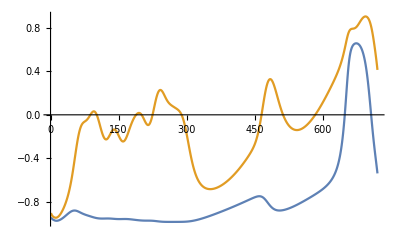
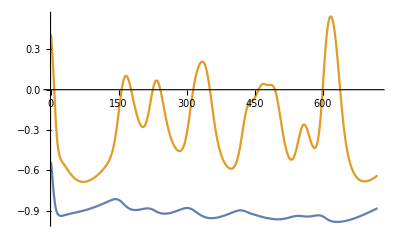
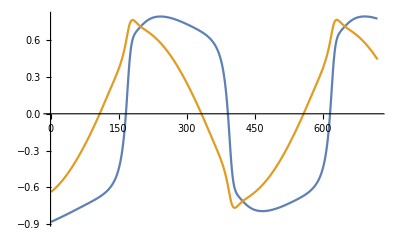
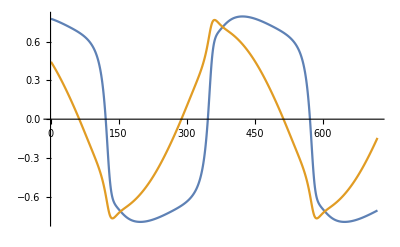
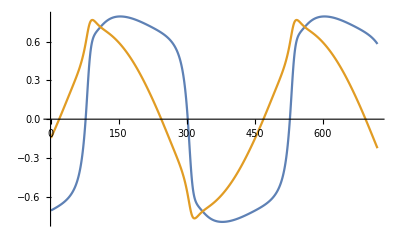
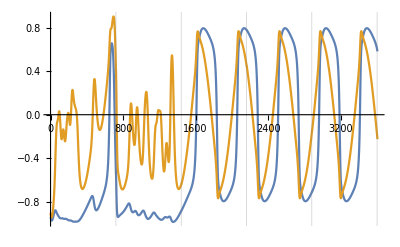
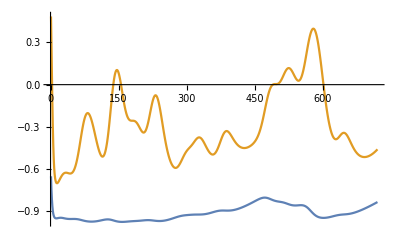
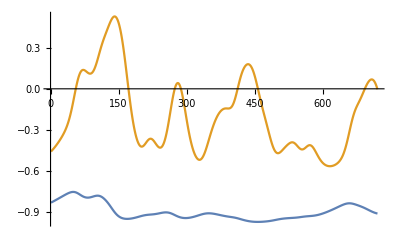
timeI | {{0,30},1} | {{30,60},1} | {{60,90},0} | {{90,120},0} | {{120,150},0} | all
2/5 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
4/5 | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

mean: | {{0,30},1} | {{30,60},1} | {{60,90},0} | {{90,120},0} | {{120,150},0}
2/5 | -0.528063 | -0.803034 | -0.0191002 | -0.0694483 | 0.140249
4/5 | -0.744821 | -0.767344 | -0.106919 | 0.0139582 | 0.0729919

rms: | {{0,30},1} | {{30,60},1} | {{60,90},0} | {{90,120},0} | {{120,150},0}
2/5 | 0.798811 | 0.859837 | 0.729537 | 0.724339 | 0.71798
4/5 | 0.839948 | 0.838541 | 0.730054 | 0.727927 | 0.724116
max %diff | 0.0502053 | 0.025078 | 0.000708326 | 0.00494064 | 0.00850923

```mathematica
With[{means=Table[Map[Function[table,Mean[Flatten[table]]],statesLabeledAll[[;;,conditionIdx,;;,1]]],{conditionIdx,Length[freqs]}]},
Grid[ArrayFlatten[{{{{"mean:"}},{timeIsLabeled}},{Transpose[{Join[freqs,{(*"max %diff"*)}]}],Join[means,{(*Map[Function[list,2(Max[list]-Min[list])/(Max[list]+Min[list])],Transpose[means]]*)}]}}]]]
With[{rmss=Table[Map[Function[table,Sqrt[Mean[Flatten[table^2]]]],statesLabeledAll[[;;,conditionIdx,;;,1]]],{conditionIdx,Length[freqs]}]},
Grid[ArrayFlatten[{{{{"rms:"}},{timeIsLabeled}},{Transpose[{Join[freqs,{"max %diff"}]}],Join[rmss,{Map[Function[list,2(Max[list]-Min[list])/(Max[list]+Min[list])],Transpose[rmss]]}]}}]]]
```

```mathematica
trainingInstanceN=Round[instanceN*0.5];
timeIIdxsLast=Map[Function[boole,Last[Position[timeIsLabeled[[;;,2]],boole][[;;,1]]]],classifiedExternalConditions];
classifiers=Table[Classify[Flatten[statesLabeledAll[[timeIIdxsLast[[classifierIdx]],;;,1;;trainingInstanceN]],Length[timeIIdxsLast]],Method->"LogisticRegression"],{classifierIdx,Length[timeIIdxsLast]}];
testResults=Table[Table[Table[Table[{statesLabeledAll[[timeILabeledIdx,conditionIdx,instanceIdx,2]],classifiers[[classifierIdx]][statesLabeledAll[[timeILabeledIdx,conditionIdx,instanceIdx,1]]]},{instanceIdx,trainingInstanceN+1,instanceN}],{timeILabeledIdx,Length[timeIsLabeled]}],{conditionIdx,Length[freqs]}],{classifierIdx,Length[timeIIdxsLast]}];
```

```mathematica
errors=Table[Table[{{timeIsLabeled[[timeIIdxsLast[[classifierIdx]]]],freqs[[conditionIdx]]},Table[testResults[[classifierIdx,conditionIdx,timeILabeledIdx,;;,2]]-testResults[[classifierIdx,conditionIdx,timeILabeledIdx,;;,1]],{timeILabeledIdx,Length[timeIsLabeled]}]},{conditionIdx,Length[freqs]}],{classifierIdx,Length[timeIIdxsLast]}];
errorRates=Table[Table[{errors[[classifierIdx,conditionIdx,1]],Table[Mean[Map[Function[x,Boole[x≠0]],errors[[classifierIdx,conditionIdx,2,timeILabeledIdx]]]],{timeILabeledIdx,Length[timeIsLabeled]}]},{conditionIdx,Length[freqs]}],{classifierIdx,Length[timeIIdxsLast]}];
```

{Classifier information
Data type | NumericalTensor (size: ××500721)
Classes | ,,2/54/5
Accuracy | (90.5.) %
Method | LogisticRegression
Single evaluation time | 3.3 s/example
Batch evaluation speed | 0.317 examples/s
Loss | 0.297 ± 0.037
Model memory | 114. MB
Training examples used | 20 examples
Training time | 57.2 s,Classifier information
Data type | NumericalTensor (size: ××500721)
Classes | ,,2/54/5
Accuracy | (90.5.) %
Method | LogisticRegression
Single evaluation time | 3.66 s/example
Batch evaluation speed | 0.289 examples/s
Loss | 0.297 ± 0.037
Model memory | 115. MB
Training examples used | 20 examples
Training time | 57.7 s}

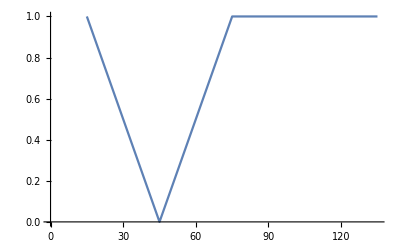
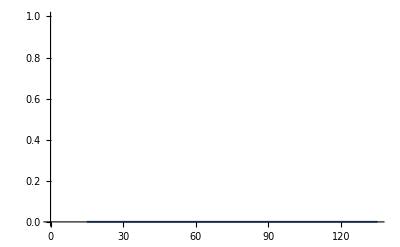
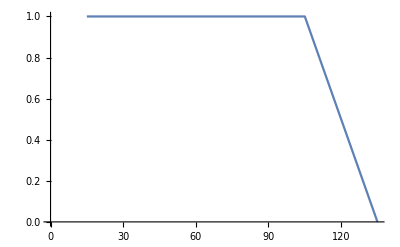
{train,test} | {{{30,60},1},2/5} | {{{30,60},1},4/5} | {{{120,150},0},2/5} | {{{120,150},0},4/5}
%error | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Map[Information,classifiers]
(*With[{errorRatesFlatten=Flatten[errorRates,1]},
{Grid[ArrayFlatten[{{{{{"cla","con"}}},{timeIsLabeled}},{errorRatesFlatten[[;;,{1}]],errorRatesFlatten[[;;,2]]}}]],Map[Function[list,ListPlot[list,Joined->True,PlotRange->{0,1}]],errorRatesFlatten[[;;,2]]]}]*)
With[{errorRatesFlatten=Flatten[errorRates,1],times=Map[Mean,timeIsLabeled[[;;,1]]]},
Grid[{Join[{{"train","test"}},errorRatesFlatten[[;;,1]]],Join[{"%error"},Map[Function[list,ListPlot[Transpose[{times,list}],Joined->True,PlotRange->{0,1}]],errorRatesFlatten[[;;,2]]]]}]]
```

```mathematica
prs=Table[Table[Table[0,instanceN],Length[timeIsLabeled]],Length[freqs]];
Do[Do[Do[prs[[conditionIdx,timeILabeledIdx,instanceIdx]]=participationRatio[Map[Variance,Transpose[PrincipalComponents[Transpose[statesLabeledAll[[timeILabeledIdx,conditionIdx,instanceIdx,1]]]]]]],
{instanceIdx,instanceN}],{timeILabeledIdx,Length[timeIsLabeled]}],{conditionIdx,Length[freqs]}]
rotationEv=Inverse[Transpose[Eigenvectors[connectivity]]];
statesEvAll=Table[Table[Table[rotationEv.statesLabeledAll[[timeILabeledIdx,conditionIdx,instanceIdx,1]],{instanceIdx,instanceN}],{conditionIdx,Length[freqs]}],{timeILabeledIdx,Length[timeIsLabeled]}];
prsEv=Table[Table[Table[0,instanceN],Length[timeIsLabeled]],Length[freqs]];
Do[Do[Do[prsEv[[conditionIdx,timeILabeledIdx,instanceIdx]]=participationRatio[Map[Variance,statesEvAll[[timeILabeledIdx,conditionIdx,instanceIdx]]]],
{instanceIdx,instanceN}],{timeILabeledIdx,Length[timeIsLabeled]}],{conditionIdx,Length[freqs]}]
prsNatural=Table[Table[Table[0,instanceN],Length[timeIsLabeled]],Length[freqs]];
Do[Do[Do[prsNatural[[conditionIdx,timeILabeledIdx,instanceIdx]]=participationRatio[Map[Variance,statesLabeledAll[[timeILabeledIdx,conditionIdx,instanceIdx,1]]]],
{instanceIdx,instanceN}],{timeILabeledIdx,Length[timeIsLabeled]}],{conditionIdx,Length[freqs]}]
```

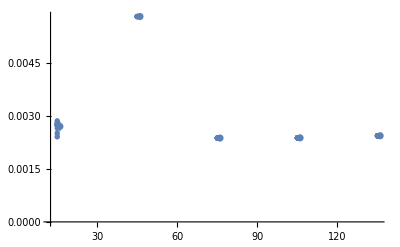
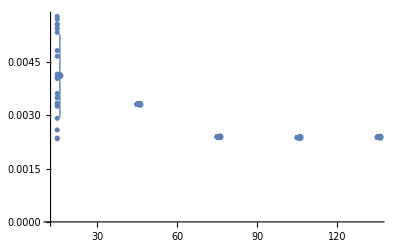
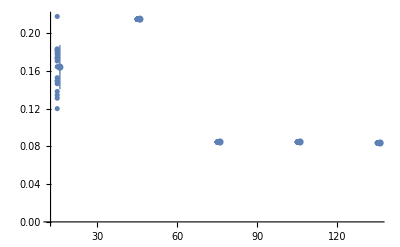
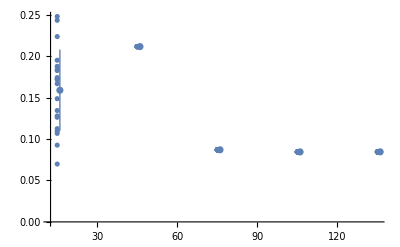
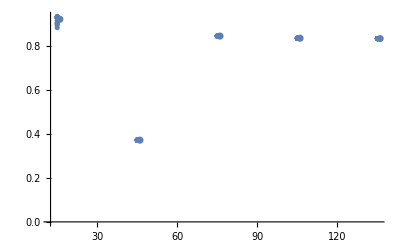
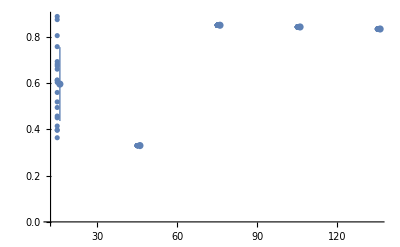
| 2/5 | 4/5
pca | -Graphics- | -Graphics-
ev | -Graphics- | -Graphics-
natural | -Graphics- | -Graphics-

```mathematica
With[{timeMeans=Table[Mean[timeIsLabeled[[timeILabeledIdx,1]]],{timeILabeledIdx,Length[timeIsLabeled]}]},Grid[Join[{Join[{" "},freqs]},Map[Function[table,Apply[Join,table]],Transpose[{{{"pca"},{"ev"},{"natural"}},Map[Function[table,Table[Show[ListPlot[Apply[Join,Table[Transpose[{timeMeans[[timeILabeledIdx]]*Table[1,instanceN],table[[conditionIdx,timeILabeledIdx]]}],{timeILabeledIdx,Length[timeIsLabeled]}]],PlotRange->All],ListPlot[Table[{timeMeans[[timeILabeledIdx]]+1,Around[Mean[table[[conditionIdx,timeILabeledIdx]]],StandardDeviation[table[[conditionIdx,timeILabeledIdx]]]]},{timeILabeledIdx,Length[timeIsLabeled]}]]],{conditionIdx,Length[freqs]}]],{prs,prsEv,prsNatural}]}]]]]]
```

#### classifiability - different connectivityExternals